```mathematica
SetDirectory[NotebookDirectory[]];
Get["eigenfaces-algorithm.m"]
```

```mathematica
makeGrid[trainingData_,testData_,numEF_]:=Module[{},
neutralFaces=trainingData[[All,1]];
normalizedFaces=Map[#-Mean[#]&, Flatten/@trainingData[[All,1]]];
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];
trainingFaces=Map[eigenCompress[#,eigenfaces,numEF]&,normalizedFaces];
Grid@Table[Join[{Image[face[[1]]],"→"},matches=recognizeFace[face[[1]],numEF,1][[1]];trainingData[[matches,2]]],{face,testData}]
]
```

```mathematica
FOM[trainingData_,testData_,numEF_/;NumberQ[numEF]]:=Module[{},
FOM[trainingData,testData,{numEF,numEF}][[1]]
]
```

```mathematica
FOM[trainingData_,testData_,{numEFmin_,numEFmax_}]:=Module[{},
FOM[trainingData,trainingData,testData,{numEFmin,numEFmax}]
]
```

```mathematica
FOM[trainingData_List,eigenTraining_List,testData_List,{numEFmin_,numEFmax_}]:=Module[{allTrainingFaces,successpercent,successpercents},
neutralFaces=eigenTraining[[All,1]];
normalizedFaces=Map[#-Mean[#]&, Flatten/@eigenTraining[[All,1]]];
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];

(* Switch to using full training data *)
normalizedFaces=Map[#-Mean[#]&, Flatten/@trainingData[[All,1]]];
allTrainingFaces=Map[eigenCompress[#,eigenfaces,numEFmax]&,normalizedFaces];

(* Compute the success percentages for each numEF *)
successpercents=Table[
trainingFaces=allTrainingFaces[[All,1;;numEF]];
matchesFound=Table[{face[[2]],trainingData[[recognizeFace[face[[1]],numEF,1][[1,1]]]][[2]]},{face,testData}];
successpercent=(Length@Cases[matchesFound,{x_,x_}])/(Length@matchesFound),{numEF,numEFmin,numEFmax}];
Return[successpercents]
]
```

```mathematica
Table[i,{i,10,5,-1}]
```

{10,9,8,7,6,5}

# Neutral faces training

```mathematica
labelledFaces=MapThread[Labeled[#1,#2]&,{images,Catenate@Transpose@ConstantArray[names,8]}];
```

## Train on 43, test on 301 (sampled)

```mathematica
training=labelledFaces[[1;;344;;8]];testing=labelledFaces[[Complement[Range[344],Range[1,344,8]]]];
```

```mathematica
data=Table[FOM[training,testing[[s;;All;;7]],{1,43}],{s,1,7}];
Dimensions@data
```

{7,43}

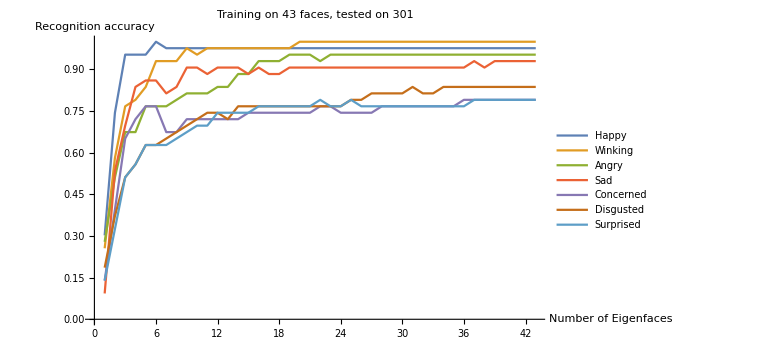

```mathematica
ListLinePlot[data,PlotRange->{{0,All},{0,1}},PlotLegends->emotions[[2;;8]],ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"},PlotLabel->"Training on "<>ToString@Length@training<>" faces, tested on "<>ToString@Length@testing]
Export["fewtrain.png",%];
```

## Train on 301, test on 43 (sampled)

```mathematica
training2=labelledFaces[[Complement[Range[344],Range[7,344,8]]]];
testing2=labelledFaces[[7;;344;;8]];
```

```mathematica
data2=FOM[training,training2,testing2,{1,43}];
Dimensions@data2
```

{43}

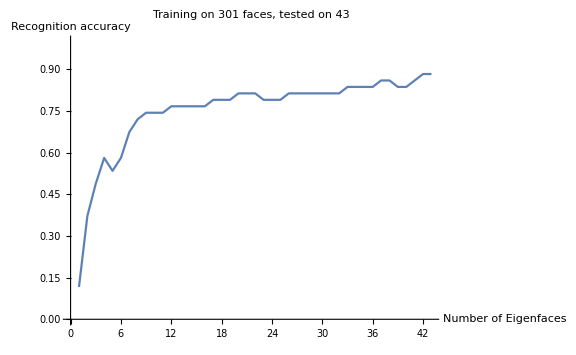

```mathematica
ListLinePlot[data2,PlotRange->{{0,All},{0,1}},ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"},PlotLabel->"Training on "<>ToString@Length@training2<>" faces, tested on "<>ToString@Length@testing2]
Export["manytrain.png",%];
```

```mathematica
makeGrid[training2,testing2,All]
```

-Graphics- | → | Ariana
-Graphics- | → | Danny
-Graphics- | → | Charlie
-Graphics- | → | Chloe
-Graphics- | → | Chris
-Graphics- | → | Danny
-Graphics- | → | David
-Graphics- | → | Dhash
-Graphics- | → | Diego
-Graphics- | → | Emily
-Graphics- | → | Eric
-Graphics- | → | Gwen
-Graphics- | → | Harper
-Graphics- | → | Isaac
-Graphics- | → | Izzy
-Graphics- | → | Jared
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | Jonah
-Graphics- | → | Kaitlyn
-Graphics- | → | Kevin
-Graphics- | → | Lauren
-Graphics- | → | Joseph
-Graphics- | → | Lydia
-Graphics- | → | Margo
-Graphics- | → | Mark
-Graphics- | → | Mary
-Graphics- | → | Max
-Graphics- | → | Mica
-Graphics- | → | Nathan
-Graphics- | → | Paige
-Graphics- | → | Rebecca
-Graphics- | → | Regina
-Graphics- | → | Ruby
-Graphics- | → | Sam
-Graphics- | → | Sarah
-Graphics- | → | Sean
-Graphics- | → | Siddhartan
-Graphics- | → | Min
-Graphics- | → | Sung
-Graphics- | → | Taylor
-Graphics- | → | Uma
-Graphics- | → | Willem

```mathematica
emotions
```

{Neutral,Happy,Winking,Angry,Sad,Concerned,Disgusted,Surprised}

## Work with fewer people

```mathematica
Length@images
```

344

```mathematica
training3=labelledFaces[[1;;40;;8]];
testing3=labelledFaces[[Complement[Range[40],Range[40,8]]]];
training4=labelledFaces[[Complement[Range[40],Range[3,40,8]]]];
testing4=labelledFaces[[3;;40;;8]];
```

### Train on few

```mathematica
data3=FOM[training3,training3,testing3,{1,5}];
Dimensions@data3
```

{5}

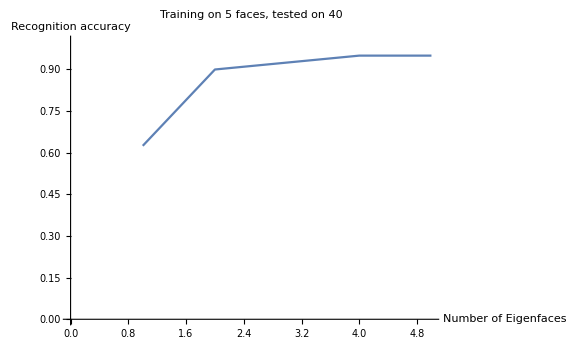

```mathematica
ListLinePlot[data3,PlotRange->{{0,All},{0,1}},ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"},PlotLabel->"Training on "<>ToString@Length@training3<>" faces, tested on "<>ToString@Length@testing3]
```

```mathematica
makeGrid[training2,testing2,All];
```

$Aborted

```mathematica
emotions
```

{Neutral,Happy,Winking,Angry,Sad,Concerned,Disgusted,Surprised}

### Train on many

```mathematica
data3=FOM[training3,training4,testing4,{1,5}];
Dimensions@data3
```

{5}

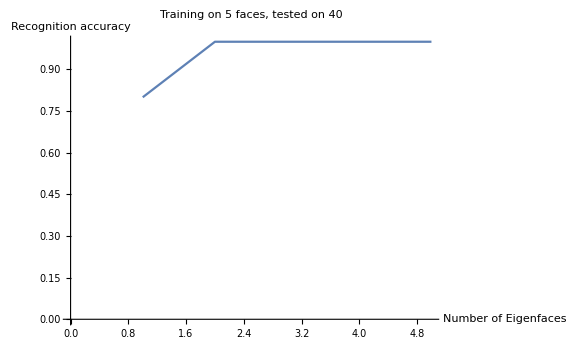

```mathematica
ListLinePlot[data3,PlotRange->{{0,All},{0,1}},ImageSize->Large,AxesLabel->{"Number of Eigenfaces","Recognition accuracy"},PlotLabel->"Training on "<>ToString@Length@training3<>" faces, tested on "<>ToString@Length@testing3]
```

```mathematica
makeGrid[training2,testing2,All]
```

-Graphics- | → | Ariana
-Graphics- | → | Danny
-Graphics- | → | Charlie
-Graphics- | → | Chloe
-Graphics- | → | Chris
-Graphics- | → | Danny
-Graphics- | → | David
-Graphics- | → | Dhash
-Graphics- | → | Diego
-Graphics- | → | Emily
-Graphics- | → | Eric
-Graphics- | → | Gwen
-Graphics- | → | Harper
-Graphics- | → | Isaac
-Graphics- | → | Izzy
-Graphics- | → | Jared
-Graphics- | → | John
-Graphics- | → | John
-Graphics- | → | Jonah
-Graphics- | → | Kaitlyn
-Graphics- | → | Kevin
-Graphics- | → | Lauren
-Graphics- | → | Joseph
-Graphics- | → | Lydia
-Graphics- | → | Margo
-Graphics- | → | Mark
-Graphics- | → | Mary
-Graphics- | → | Max
-Graphics- | → | Mica
-Graphics- | → | Nathan
-Graphics- | → | Paige
-Graphics- | → | Rebecca
-Graphics- | → | Regina
-Graphics- | → | Ruby
-Graphics- | → | Sam
-Graphics- | → | Sarah
-Graphics- | → | Sean
-Graphics- | → | Siddhartan
-Graphics- | → | Min
-Graphics- | → | Sung
-Graphics- | → | Taylor
-Graphics- | → | Uma
-Graphics- | → | Willem

## Misc

```mathematica
emotions
```

{Neutral,Happy,Winking,Angry,Sad,Concerned,Disgusted,Surprised}

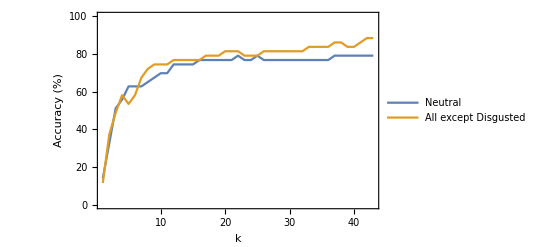

../pictures/testB.eps

```mathematica
ListLinePlot[100*{data[[7]],data2},PlotRange->{All,{0,100}},Axes->None,FrameTicks->{{All,All},{All,None}},PlotLegends->Placed[{"Neutral","All except Disgusted"},Above],Frame->True,FrameLabel->{"k","Accuracy (%)"}]
Export["../pictures/testB.eps",%]
```

```mathematica
training3=labelledFaces[[Complement[Range[344],Range[2,344,8]]]];
testing3=labelledFaces[[2;;344;;8]];
```

```mathematica
data3=FOM[training,training3,testing3,{1,43}];
Dimensions@data2
```

{43}

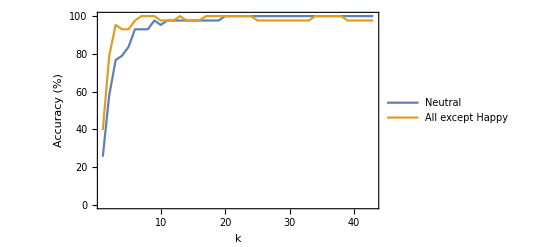

../pictures/testA.eps

```mathematica
ListLinePlot[100*{data[[2]],data3},PlotRange->{All,{0,100}},Axes->None,FrameTicks->{{All,All},{All,None}},PlotLegends->Placed[{"Neutral","All except Happy"},Above],Frame->True,FrameLabel->{"k","Accuracy (%)"}]
Export["../pictures/testA.eps",%]
```